## Illustration of Theorem 2, Part 3, p. 102

Part 3 of Theorem 2 on p. 102 says that if

lim_(x->a) g(x)=l and l≠0, then lim_(x->a) 1/(g(x))=1/l.

In words, succinctly and casually, “the limit of the inverse is the inverse of the limit.”

Let’s illustrate the theorem with a specific example.

### The Function

```mathematica
g[x_]:=Cos[x]
```

```mathematica
a=Pi/3;
```

```mathematica
plot=Plot[g[x],{x,-3 Pi/2,3 Pi/2},AspectRatio->2/3];
point=Point[{a,g[a]}];
```

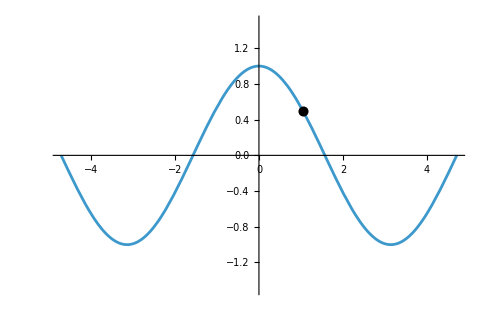

```mathematica
Show[plot,Graphics[Style[point,PointSize[0.015]]],PlotRange->{-1.5,1.5}]
```

### The Inverse Function

```mathematica
gInverse[x_]:=If[g[x]==0,1000,1/g[x]]
```

```mathematica
plot2=Plot[gInverse[x],{x,-3 Pi/2,3 Pi/2},AspectRatio->4/3];
point2=Point[{a,gInverse[a]}];
```

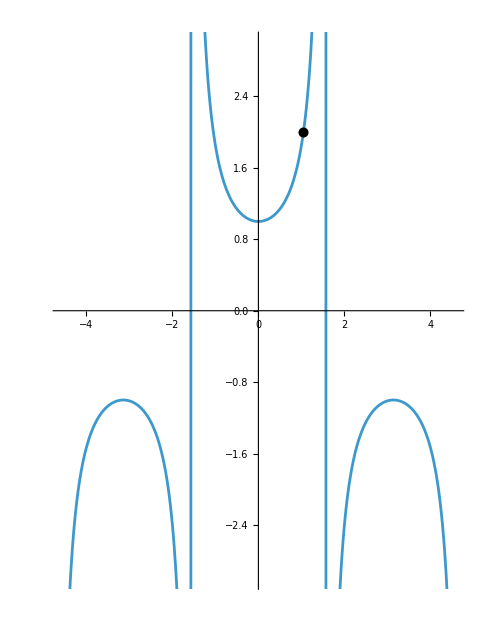

```mathematica
Show[plot2,Graphics[Style[point2,PointSize[0.015]]],PlotRange->{-3,3}]
```